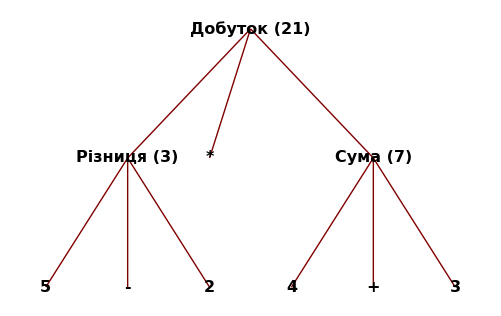

```mathematica
lbls={"Добуток (21)","Різниця (3)", "5","-","2","Сума (7)","4","+","3","*",,,};
TreePlot[
{1->2,1->10,1->6,2->3,2->4,2->5,6->7,6->8,6->9},
VertexRenderingFunction->
(Text[Pane[Style[lbls[[#2]],16,Bold],ImageMargins->3],#1,Background->White]&)]
```

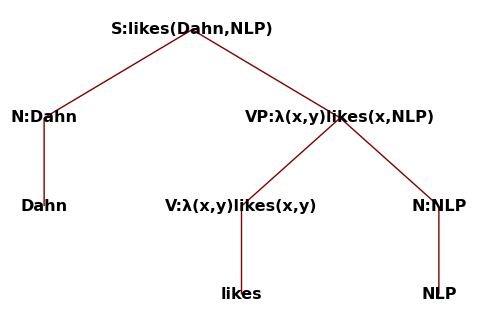

```mathematica
lbls=StringSplit["S:likes(Dahn,NLP) N:Dahn Dahn VP:λ(x,y)likes(x,NLP) V:λ(x,y)likes(x,y) likes N:NLP NLP"];
TreePlot[
{1->2,2->3,1->4,4->5,5->6,4->7,7->8},
VertexRenderingFunction->
(Text[Pane[Style[lbls[[#2]],16,Bold],ImageMargins->3],#1,Background->White]&)
,LayerSizeFunction->(0.3&)]
```

```mathematica
(*wow hax*)
Export[FileNameJoin@{NotebookDirectory[],"rain_symbol.png"},RemoveBackground[Import["/home/i/shelf/data/img/rain.png"]]]
```

/home/i/pos/rain_symbol.png

```mathematica
obs[l_,i_]:=GraphicsColumn[{
Text@Style[l,Bold]
,Import[i]}
,Automatic,Scaled[-.9],Frame->All]
obs[l_,i_]:=Graphics[{Raster[ImageData[Import[i],DataReversed->True]],
Inset@Text[Pane[Style[l,14,Bold,FontFamily->"DejaVu Sans"],ImageMargins->{{10,10},{1,1}}],Background->RGBColor[1,1,1,.7]]}]
lbls={Graphics@{(*White,EdgeForm@Black,Disk[],Black,*)Text@Style["Початок",14,Bold,FontFamily->"DejaVu Sans"]}
,Import["/home/i/shelf/data/img/sun.png"]
,Import["/home/i/pos/rain_symbol.png"]
,obs["Навчання","/home/i/shelf/data/img/book-stack.png"]
,obs["Прогулянка","/home/i/shelf/data/img/oak-clipart.png"]
,obs["Прибирання","/home/i/shelf/data/img/broom-clipart.png"]
};
TreePlot[{
{1->2,.6},{1->3,.4}
,{2->2,.7},{2->3,.6}
,{3->3,.6},{3->2,.4}
,{2->4,.1},{2->5,.4},{2->6,.5}
,{3->4,.6},{3->5,.3},{3->6,.1}
},Top,1
,SelfLoopStyle->.5
,EdgeRenderingFunction->(Block[{p=#1,t=.5,edge},
If[#2⟦2⟧>3,p⟦2⟧+={.37,0};t-=.11;
edge={Dashed,Line[p⟦{1,-1}⟧]},
edge={Arrowheads@.03,Arrow[BSplineCurve[p],.22]}];
edge~Join~{
Text[Pane[Style[#3,12,Bold],ImageMargins->3],BSplineFunction[p]@t,Background->White]}]&)
,VertexRenderingFunction->(Block[{p,s=.2},
p=#1;If[#2>3,p=p+{.37,0};s+=.1];
{White,EdgeForm@Black,Disk[p,s],Black,Inset[lbls⟦#2⟧,p,Center,s+.08]}]&)
,ImageSize->700]
```

-Graphics-
-Graphics-

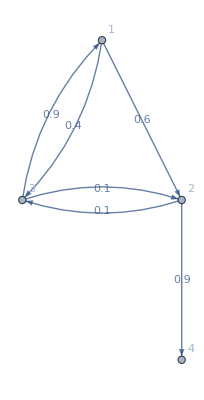

```mathematica
Graph[Labeled@@@{
{1->2,.6},{1->3,.4}
,{2->3,.1},{2->4,.9}
,{3->1,.9},{3->2,.1}
}/.Rule->DirectedEdge
,GraphLayout->"LayeredEmbedding"
,VertexLabels->"Name"]
```